```mathematica
(* Mathematica Notebook demonstrating usage of DPG packages. *)
(* Created in Mathematica 12.0 *)
(* :Author: Shubha Raj Kharel *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Degree Preserving Network Growth (DPG)

## Grow a network with DPG process

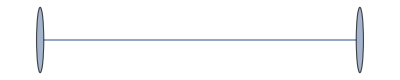
```mathematica
Needs["DPG`"]
seedGraph=-Graphics-;
degreeSequence={1,2,2,3 ,3,4,4};
{finalG,phantomV}=DPGrow[seedGraph,degreeSequence];
Graph[finalG,GraphLayout->"SpringElectricalEmbedding"]
```

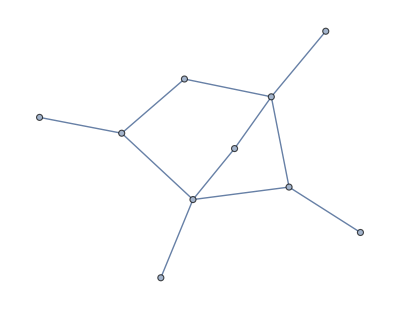

## DPG models

```mathematica
Needs["DPGModels`"];
```

## MaxDPG

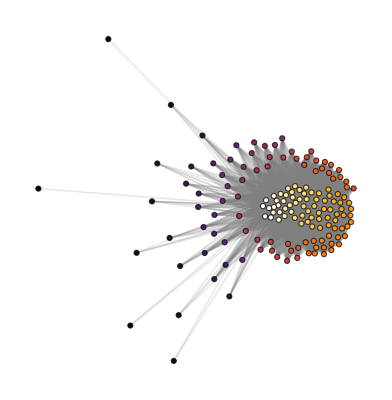

```mathematica
(*Grow an sigle edge by adding 150 nodes through maxDPG process.*)
{g, phantomV} = maxDPG[CompleteGraph[2], 150];

Graph[g, GraphLayout -> "SpringElectricalEmbedding"
 	,VertexStyle -> Table[i -> ColorData["SunsetColors"][i/VertexCount@g], {i, VertexList@g}]
 	, EdgeStyle -> Opacity[0.2, Gray]]
```

## RndDPG

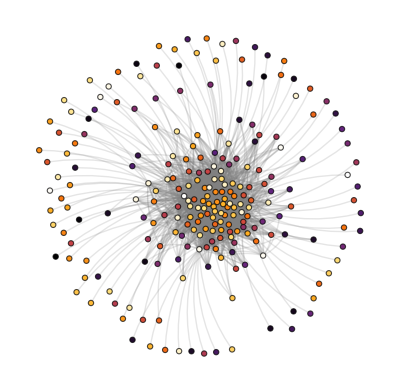

```mathematica
{g,newPhantomV} = rndDPG[CompleteGraph[2],150];

Graph[g,GraphLayout->"GravityEmbedding"
	,VertexStyle->Table[i->ColorData["SunsetColors"][i/VertexCount@g],{i,VertexList@g}]
	,EdgeStyle->Opacity[0.2,Gray]]
```

## LinearDPG

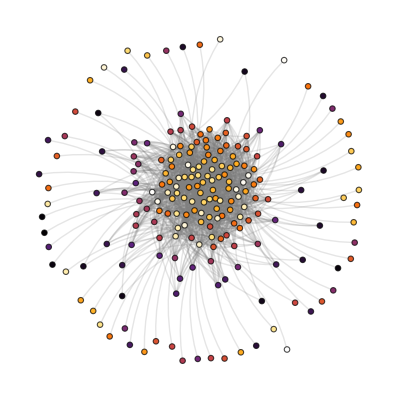

```mathematica
{g,newPhantomV} = linearDPG[CompleteGraph[2],150,0.3];

Graph[g,GraphLayout->"GravityEmbedding"
	,VertexStyle->Table[i->ColorData["SunsetColors"][i/VertexCount@g],{i,VertexList@g}]
	,EdgeStyle->Opacity[0.2,Gray]]
```

## Regular DPG

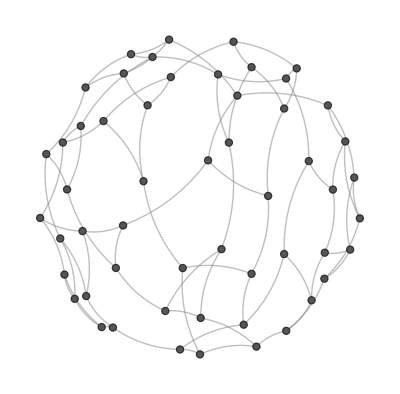

```mathematica
{g,newPhantomV} = regularDPG[CompleteGraph[4],50,3];

Graph[g,GraphLayout->"GravityEmbedding",VertexStyle-> Darker@Gray,EdgeStyle->Opacity[0.5,Gray]]
```

## Inverse DPG (Degree preserving reduction)

## Removes vertices for graph using inverse DPG process

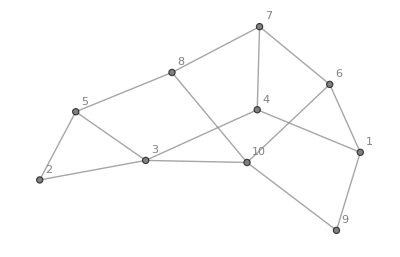
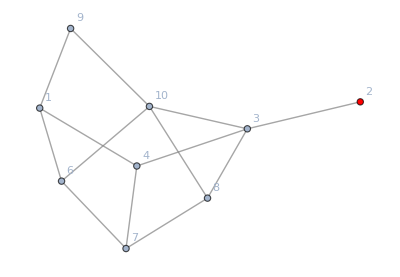
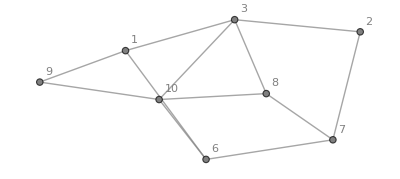
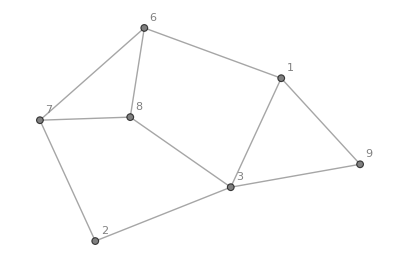
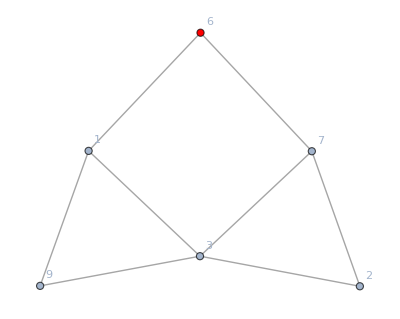
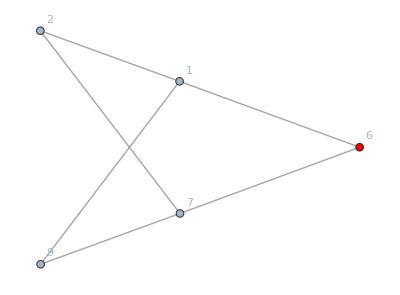
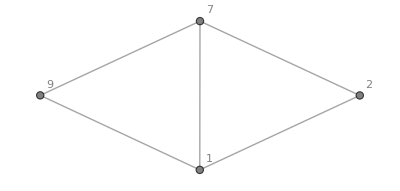
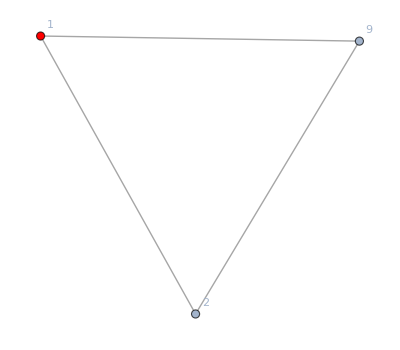
-Graphics- | Removing 5... | 
-Graphics- | Removing 4... | 
-Graphics- | Removing 10... | 
-Graphics- | Removing 8... | 
-Graphics- | Removing 3... | 
-Graphics- | Removing 6... | 
-Graphics- | Removing 7... | 
-Graphics- |  |

```mathematica
Get["InvDPG`"];

g=RandomGraph[{10,15}];

(*Reap stores intermediate state of graph during inverser DPG process*)
{g0,{gList}}=Reap@inverseDPG[g,Infinity];

(*Print all inverse DPG step. Red nodes have phantom neighbour.*)
TableForm@gList
```

## Network optimization

## Find weighted independent edges

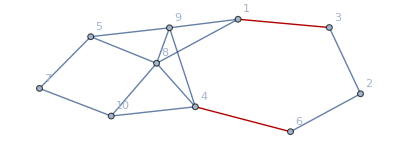

1<->3 | 19.
1<->8 | 16.5
1<->9 | 11.1667
2<->3 | 10.3333
2<->6 | 14.3333
4<->6 | 23.
4<->8 | 9.83333
4<->9 | 10.8333
4<->10 | 13.
5<->7 | 8.66667
5<->8 | 10.3333
5<->9 | 10.3333
7<->10 | 11.3333
8<->9 | 3.
8<->10 | 10.3333

```mathematica
Get["WeightedMatching`"];

(*Function that will assign weight to the edges*)
WBetCentrality[g_,d_]:=EdgeBetweennessCentrality[g];

(*Generate raondom graph*)
g=RandomGraph[{10,15},VertexLabels->Automatic];

(*Find matching that tries to maximize the the total weight*)
M=findWeightedIndpendentEdges[g,WBetCentrality,2];
HighlightGraph[g,M]

(*Print table of centrality of all edges for comparision.*)
TableForm@Transpose@{EdgeList[g],EdgeBetweennessCentrality[g]}
```

## Grow graph using DPG to optimize assortativity

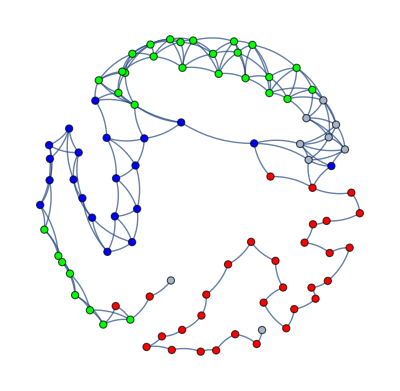

Assortativty =0.910492

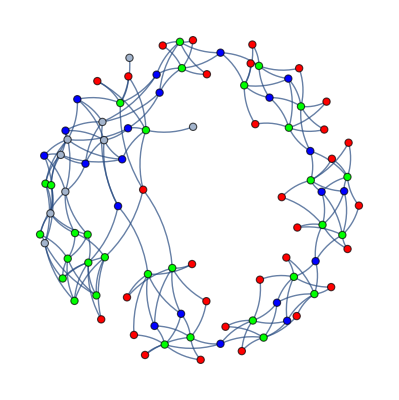

Assortativty =-0.792582

```mathematica
Get["DPGAssortativity`"];

(*degree sequence of from which two graphs with different assortativity will be grown*)
degreeSequence = ConstantArray[2,30]~Join~ConstantArray[4,30]~Join~ConstantArray[6,30];

(*DPG grow graph while increasing  degree assortativity*)
{finalG,PhantomV}=DPGrowAssortativity[CompleteGraph[2],degreeSequence];

(*Print high assortativity graph*)
Graph[finalG,GraphLayout->"GravityEmbedding",VertexStyle->Join[Join[Table[i->Red,{i,3,33}],Table[i->Blue,{i,34,54}]],Table[i->Green,{i,55,85}]]]
Print["Assortativty =" <> ToString@N@GraphAssortativity@finalG];

(*DPG grow graph while decreasing assortativity*)
{finalG,PhantomV}=DPGrowAssortativity[CompleteGraph[2],degreeSequence,False];

(*Print low assortativity graph*)
Graph[finalG,GraphLayout->"GravityEmbedding",VertexStyle->Table[i->Red,{i,3,33}]~Join~Table[i->Blue,{i,34,54}]~Join~Table[i->Green,{i,55,85}]]
Print["Assortativty =" <> ToString@N@GraphAssortativity@finalG];
```

## Network optimization through degree preserving rewiring

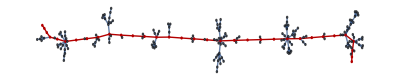

Graph Diameter = 32

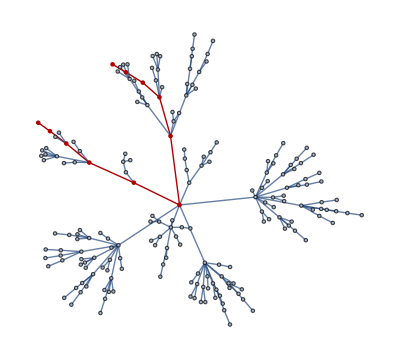

Graph Diameter = 10

```mathematica
Needs["DPR`"];

(*Generate random tree*)
g0=RandomGraph[{200,500}];
g0=Subgraph[FindSpanningTree@g0,First@ConnectedComponents@FindSpanningTree@g0];

(*function used to find diameter path in undirected graph*)
findDiameterPath[g_?UndirectedGraphQ]:=Module[{d=GraphDistanceMatrix[g],u,v,pos},pos=First@Position[d,Max[d]];
{u,v}=Part[VertexList[g],pos];
PathGraph@FindShortestPath[g,u,v]]

(*Do degree preserving rewiring to increase the diamter*)
g=DPROptimize[g0,GraphDiameter,1,1000,True];
HighlightGraph[g,findDiameterPath[g]]
Print["Graph Diameter = " <>ToString@GraphDiameter[g]]

(*Do degree preserving rewiring to decrease the diameter*)
g=DPROptimize[g0,GraphDiameter,-1,1000,True];
HighlightGraph[g,findDiameterPath[g]]
Print["Graph Diameter = " <>ToString@GraphDiameter[g]]
```

## Miscellaneous

## Calculate splittance of graph

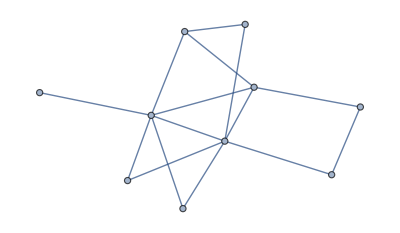

Splittance = 2

```mathematica
Needs["Splittance`"];
g = RandomGraph[{10, 15}]
Print["Splittance = " <> ToString@findSplittance@g]
```

## Find independent edges using blossom algorithm

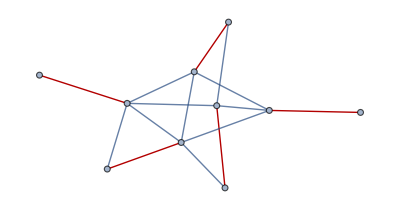

```mathematica
Needs["Blossom`"];
g=RandomGraph[{10,15}];
M=findIndependentEdges[g,{},Infinity];
HighlightGraph[g,M]
```